```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

### Definitions of the γ-compounding algebra

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

### Define parameters for simulations

```mathematica
X0 = 1;
T =100;
M = 100;
g = 21/20;
r = 9/20;
```

### Define analytical formulae

```mathematica
x[t_, g_] := X0 ⊗ Expγ[Logγ[g] t];
f[x_, b_, g_, r_] := If[b ==0, x ⊗ (g+r), x ⊗ (g-r)]
```

### Generate some trajectories

```mathematica
X = Table[0,{i,1,T+1}, {j,1,M}];
B = Table[RandomInteger[{0,1}],{i,1,T}, {j,1,M}];
For[j=1, j<= M, j++, 
X[[1,j]]= X0;
For[i=2, i<= T+1, i++,
c = B[[i-1,j]];
X[[i,j]]= N[f[X[[i-1, j]], c, g, r]];
];

];
```

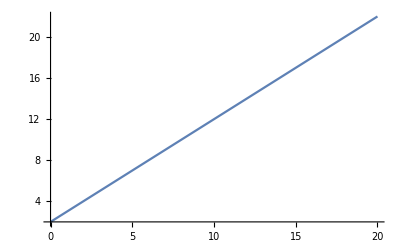

```mathematica
Plot[x[t,2] /. {X0->2, γ->1}, {t, 0, 20}, PlotRange->Full]
```

```mathematica
x[3,g +1] /. γ-> 0 // PowerExpand // FullSimplify
```

(1+g)^3 X0

```mathematica
(Log[(g+r)/(g-r)]/Log[g^2- r^2])^2 /. {g->21/20, r-> 9/20} // N
```

75.6329

```mathematica
RandomInteger[{0,1}]
```

0

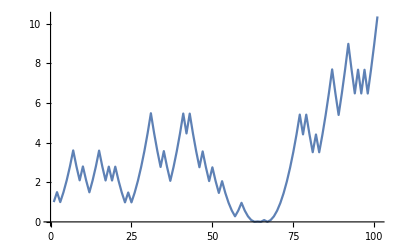

```mathematica
ListPlot[X[[1;;T+1, 1]], Joined->True]
```

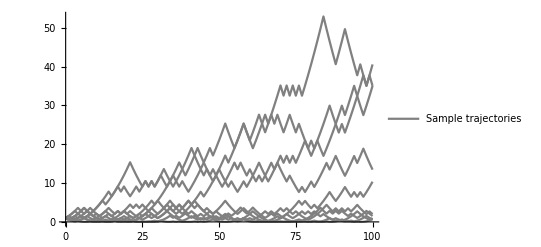

```mathematica
sampleTrajectories=TemporalData[X[[1;;T+1, 1;;10]],{Table[i-1, {i,1, T+1}]}];
p1 = ListPlot[sampleTrajectories,PlotStyle->Gray,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]]
```

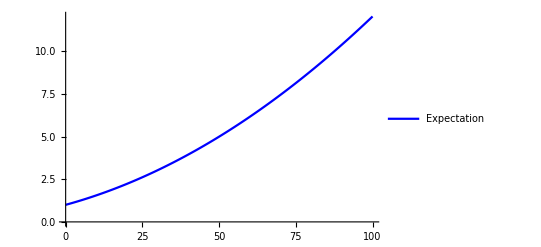

```mathematica
Ex = Table[N[x[t,g]],{t,0,T}];
expectedValue = TemporalData[Ex, {Table[i-1, {i,1, T+1}]}];
p2 = ListPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]]
```

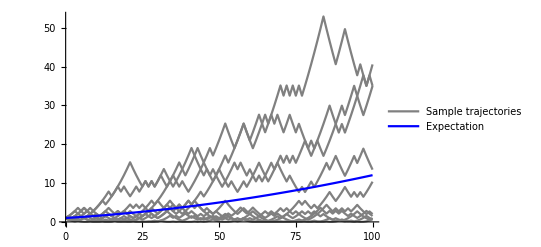

```mathematica
Show[p1,p2]
```